# Лабораторная работа №4.

## Задание 1.

Создайте интерактивную панель для ввода пользователем концов двух отрезков с помощью мыши. Отобразите отрезки  красным цветом, если они пересекаются и зелёным в противном случае.

```mathematica
DynamicModule[{pointlist={}},Column[{Button["Refresh",pointlist={}],ClickPane[Framed@Dynamic@Graphics[{PointSize@0.02,Point/@pointlist,Black,Line/@Partition[pointlist,2]},PlotRange->{{0,10},{0,10}},ImageSize->500],AppendTo[pointlist,#]&]}]]
```

```mathematica
(*Решение и ход работы*)
lineEq[pt1_,pt2_]:=With[{vect=pt2-pt1},{(x-pt1[[1]])vect[[2]]-vect[[1]](y-pt1[[2]])}]
```

```mathematica
p1={0,0};
p2={2,1};
p3={-1,-3};
p4={0,2};
```

```mathematica
l1=lineEq[p1,p2]
l2=lineEq[p3,p4]
```

{x-2 y}

{-3+5 (1+x)-y}

```mathematica
Solve[l1==0&&l2==0,{x,y}]
```

{{x→-4/9,y→-2/9}}

```mathematica
(*Точка пересечения двух прямых*)
getCommonPt[pt1_,pt2_,pt3_,pt4_]:=Block[{answer=Solve[lineEq[pt1,pt2]==0&&lineEq[pt3,pt4]==0,{x,y}]},Return[{x,y}/.answer[[1]]]]
```

```mathematica
(*Пробую считать расстояние*)
N[Norm[getCommonPt[{-2,0},{0,2},{0,0},{2,4}]-p2]+Norm[getCommonPt[{-2,0},{0,2},{0,0},{2,4}]-p3]]
```

10.6158

```mathematica
(*Принадлежит ли точка отрезку*)
sectorPointQ[pt1_,pt2_,cpt_]:=If[And[N[Norm[pt2-pt1]]==N[Norm[cpt-pt1]+Norm[cpt-pt2]]],True,False]
```

```mathematica
(*Пересекаются ли отрезки*)
segmentsIntersectQ[pt1_,pt2_,pt3_,pt4_]:=Block[{cpt=getCommonPt[pt1,pt2,pt3,pt4]},Return[sectorPointQ[pt1,pt2,cpt]&&sectorPointQ [pt3,pt4,cpt]]]
```

```mathematica
(*Проверяю*)
sectorPointQ[{-2,0},{0,2},{2,4}]
segmentsIntersectQ[{-2,0},{0,2},{0,0},{2,4}]
```

False

False

```mathematica
(*Partition - разделяет список на непересекающиеся подсписки длины n.*)
DynamicModule[{pointlist={}},Column[{Button["Refresh",pointlist={}],ClickPane[Framed@Dynamic@Graphics[{PointSize@0.02,Black,If[Length[pointlist]==4,If[segmentsIntersectQ[Partition[pointlist,2][[1,1]],Partition[pointlist,2][[1,2]],Partition[pointlist,2][[2,1]],Partition[pointlist,2][[2,2]]],Red,Green],Nothing],Point/@pointlist,Line/@Partition[pointlist,2]},PlotRange->{{0,10},{0,10}},ImageSize->500],If[Length[pointlist]<4,AppendTo[pointlist,#],Nothing]&]}]]
(*Всегда иcпользовать Block лучше для наших задач*)
```

## Задание 2.

Создайте функцию, генерирующую итерации ковра серпинского. Фрактал задавайте списком точек. Отобразите точки на графической области.
Обеспечьте возможность просматривать накопление точек с помощью функции Manipulate или анимации.

```mathematica
base={{0,0},{0,1},{1,0},{1,1},{1/2,0},{1/2,1},{1,1/2},{0,1/2}}
```

{{0,0},{0,1},{1,0},{1,1},{1/2,0},{1/2,1},{1,1/2},{0,1/2}}

```mathematica
kover[base_,1]:=Flatten[{base,((base/3) [[#]]+{0,0/3})&/@Range[1,Length[base]],
((base/3) [[#]]+({0,1/3}))&/@Range[1,Length[base]],
((base/3) [[#]]+{0,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{1/3,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{1/3,0})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,0})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,1/3})&/@Range[1,Length[base]]},1]
kover[base_,n_]:=kover[Flatten[{base,((base/3) [[#]]+{0,0/3})&/@Range[1,Length[base]],
((base/3) [[#]]+({0,1/3}))&/@Range[1,Length[base]],
((base/3) [[#]]+{0,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{1/3,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{1/3,0})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,0})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,1/3})&/@Range[1,Length[base]]},1],n-1]
```

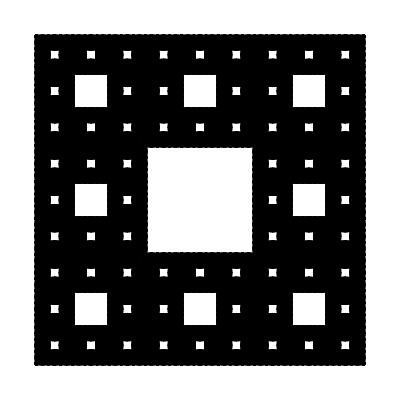

```mathematica
Graphics[{Point[kover[base,4]]}]
```

```mathematica
Manipulate[Graphics[Point[kover[base,a]]],{a,{1,2,3,4}}]
```

```mathematica
getPoint[points_]:=Block[{myPts=points},rNum=RandomInteger[{1,8}];AppendTo[points,{N[(points[[Length[points],1]]+2*base[[rNum,1]])/3],N[(points[[Length[points],2]]+2*base[[rNum,2]])/3]}]]
```

```mathematica
pts={{1,1}}
```

{{1,1}}

```mathematica
Manipulate[DynamicModule[{pts = {{1,1}}}, getPoint[pts]],{a,1,100}]
```

AppendTo::rvalue: {{1,1}} is not a variable with a value, so its value cannot be changed.

```mathematica
getPoint[pts]
getPoint[pts]
getPoint[pts]
getPoint[pts]
```

AppendTo::rvalue: {{1,1}} is not a variable with a value, so its value cannot be changed.

AppendTo[{{1,1}},{0.333333,1.}]

AppendTo::rvalue: {{1,1}} is not a variable with a value, so its value cannot be changed.

AppendTo[{{1,1}},{0.333333,0.666667}]

AppendTo::rvalue: {{1,1}} is not a variable with a value, so its value cannot be changed.

AppendTo[{{1,1}},{1.,0.666667}]

AppendTo::rvalue: {{1,1}} is not a variable with a value, so its value cannot be changed.

AppendTo[{{1,1}},{1.,0.666667}]

```mathematica
Manipulate[Graphics[{Point[base],Point[getPoint[pts,a]]}],{a,1,100}]
```

Part::partw: Part 2 of getPoint[{{1,1}}] does not exist.

Part::partw: Part 2 of getPoint[{{1.,1.}}] does not exist.

```mathematica
Graphics[{Point[base],Point[pts]}]
```

-Graphics-

```mathematica
points={{1,1}}
```

{{1,1}}

```mathematica
For[i=1,i<1000,i++,Block[{rNum=RandomInteger[{1,8}]},AppendTo[points,{N[(points[[Length[points],1]]+2*base[[rNum,1]])/3],N[(points[[Length[points],2]]+2*base[[rNum,2]])/3]}]]]
```

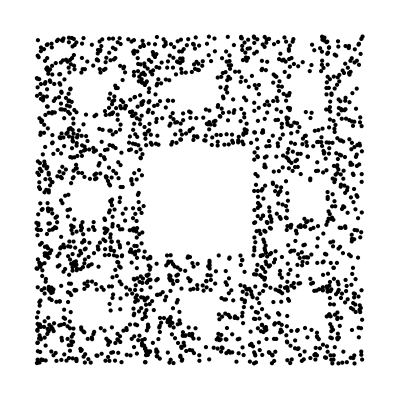

```mathematica
Graphics[{Point[points]}]
```

```mathematica
getPoints[a_]:=Block[{points={{1,1}}},For[i=1,i<a,i++,Block[{rNum=RandomInteger[{1,8}]},AppendTo[points,{N[(points[[Length[points],1]]+2*base[[rNum,1]])/3],N[(points[[Length[points],2]]+2*base[[rNum,2]])/3]}]]];Return[points]]
```

```mathematica
getPoints[10]
```

{{1,1},{0.333333,0.333333},{0.444444,0.111111},{0.814815,0.37037},{0.938272,0.790123},{0.646091,0.930041},{0.215364,0.97668},{0.405121,0.992227},{0.801707,0.997409},{0.600569,0.999136}}

```mathematica
(*Я нарисовал мух*)
```

```mathematica
Animate[
Graphics[
{Point[base],Point[getPoints[a]]
},PlotRange->{{0,1},{0,1}},Axes->True,ImageSize->500],
{a,1,1000,1}]
```

```mathematica
Manipulate[
Graphics[
{Point[base],Point[getPoints[a]]
},PlotRange->{{0,1},{0,1}},Axes->True,ImageSize->500],
{a,{10,100,1000,5000,10000}}]
```

## Задание 3

1. Создайте игру, позволяющую пользователю бродить по сетке “целых точек” (точек с целыми координатами) в некоторой графической области. отобразите траекторию и количество сделанных шагов. Управление перемещением точки осуществляется с помощью кнопок. Предусмотрите невозможность выйти за пределы области, а также невозможность пересечения траектории. Предусмотрие кнопку для рестарта игры.
	2. Добавьте на поле специальную область (чёрный квадрат), после попадания в которую игра прекращается. Пользователь получает сообщение. И происходит рестарт.

```mathematica
DynamicModule[{pointlist={{10,10}},a=True},
Grid[
{
{Button["Up",AppendTo[pointlist,Last[pointlist]+{0,1}]],Button["Down",AppendTo[pointlist,Last[pointlist]+{0,-1}]]},{Button["left",AppendTo[pointlist,Last[pointlist]+{-1,0}]],Button["rigth",AppendTo[pointlist,Last[pointlist]+{1,0}]]},
{Dynamic@Graphics[
{Red,PointSize[0.02],Point[pointlist⟦-1⟧],Dashed,,Black,Line[pointlist]},
ImageSize->300,GridLines->{Range[1,20],Range[1,20]},GridLinesStyle->LightGray,Axes->True,PlotRange->{{0,20},{0,20}}
],SpanFromLeft}
},
ItemSize->{Scaled[0.15]}]]
```